```mathematica
SetDirectory[NotebookDirectory[]];
Get["RigidBodyBp.m"]
```

Example 1 - 100bp

```mathematica
opt68bp=ReadList["minicircle_68bp_opt.txt"];
```

```mathematica
g1=opt68bp//RenderFrame/@#&//Graphics3D
```

-Graphics3D-

Example 2 - 100bp ΔLk=+1

```mathematica
opt68bplk=ReadList["minicircle_68bp_lk1_opt.txt"];
```

```mathematica
g2=opt68bplk//RenderFrame/@#&//Graphics3D
```

-Graphics3D-

```mathematica
Show[g1,g2]
```

-Graphics3D-

```mathematica
p1=opt68bp//RigidBodyParametersList;
p2=opt68bplk//RigidBodyParametersList;
```

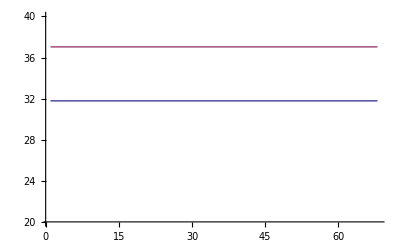

```mathematica
{p1⟦All,3⟧,p2⟦All,3⟧}//ListLinePlot[#,PlotRange->{All,{20,40}}]&
```

```mathematica
eed=ReadList["minicircle_68bp_eed_opt.txt"];
```

```mathematica
RenderFrame/@eed//Graphics3D
```

-Graphics3D-

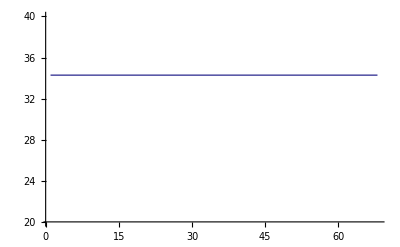

34.2857

```mathematica
RigidBodyParametersList[eed]⟦All,3⟧//ListLinePlot[#,PlotRange->{All,{20,40}}]&
RigidBodyParametersList[eed]⟦All,3⟧//Mean
```